# Optimización de Redes Bayesianas por Algoritmo Genético

### Autor: Carlos Manuel Rodríguez Martínez E-Mail: fis.carlosmanuel@gmail.com

## Resumen

Referencia:
Levine, Nicholas D., “Using Minimum Description Length for Discretization Classification of Data Modeled by Bayesian Networks” (2011). Applied Mathematics Graduate Theses & Dissertations. 21. 
https://scholar.colorado.edu/appm_gradetds/21

Friedman, Goldszmidt, “Learning Bayesian Networks from Data” (1998). Presentation.

## Inferencia

```mathematica
Parents[graph_,vertex_]:=Cases[graph, p_->vertex:>p];
PossibleValues[dataset_,attribute_]:=DeleteDuplicates[dataset[[All,attribute]]];
AttributeValues[dag_,data_,attribute_]:=Block[{parents},
parents = Parents[dag,attribute];
Map[<|"ParentValues"->#[[parents]],"Value"->#[[attribute]]|>&,data]
];
AttributeProbability[dag_,data_,node_,nodeValue_,parentValues_]:=Block[{num,den},
num = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern[{"ParentValues"->parentValues, "Value"->nodeValue}]]];
den = Length[Cases[AttributeValues[dag,data,node],KeyValuePattern["ParentValues"->parentValues]]];
If[den ≠ 0,num/den,0]
];
```

Inferencia a partir de la base de datos. Este tipo de inferencia calcula las probabilidades marginales al momento de evaluar el query. Conviene usar si se desea realizar una sola evaluación.

```mathematica
InstanceProbability[dag_,dataset_List,instance_]:=N@Apply[Times,Table[AttributeProbability[dag,dataset,i,instance[[i]],instance[[Parents[dag,i]]]],{i,1,Length[First[dataset]]}]];
BayesProbabilities[dag_,dataset_List,query_]:=Block[{queryPosition,possibleValues,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
possibleValues = PossibleValues[dataset,queryPosition];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues];
evaluated = MapThread[{#1,InstanceProbability[dag,dataset,#2]}&,{possibleValues,queryInstances}];

SortBy[evaluated,Last]
];
BayesInfer[dag_,dataset_List,query_]:=Block[{queryPosition,possibleValues,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
possibleValues = PossibleValues[dataset,queryPosition];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues];
evaluated = MapThread[{#1,InstanceProbability[dag,dataset,#2]}&,{possibleValues,queryInstances}];

First@First@MaximalBy[evaluated,Last]
];
```

Inferencia a partir de probabilidades marginales precalculadas.

```mathematica
CalculateMarginals[dag_,dataset_]:=Block[{possibleValues,marginals,n=Length[First[dataset]]},
possibleValues = Association@Table[i->PossibleValues[dataset,i],{i,1,n}];
marginals = Association@Flatten@Table[
<|"Node"->i,"Value"->val,"ParentValues"->parentValues|>->N@AttributeProbability[dag,dataset,i,val,parentValues],
{i,1,n},{val,PossibleValues[dataset,i]},{parentValues,NodeParentConfigurations[dag,dataset,i]}
];
{possibleValues,marginals}
];
InstanceProbability[dag_,marginals_Association,instance_]:=Apply[Times,Table[marginals[<|"Node"->i,"Value"->instance[[i]],"ParentValues"->instance[[Parents[dag,i]]]|>],{i,1,Length[instance]}]];

BayesProbabilities[dag_,possibleValues_,marginals_,query_]:=Block[{queryPosition,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues[queryPosition]];
evaluated = MapThread[{#1,InstanceProbability[dag,marginals,#2]}&,{possibleValues[queryPosition],queryInstances}];

SortBy[evaluated,Last]
];
BayesInfer[dag_,possibleValues_,marginals_,query_]:=Block[{queryPosition,queryInstances,evaluated},
queryPosition = First[FirstPosition[query,"?"]];
If[queryPosition=="NotFound",Return[$Failed]];
queryInstances = Map[ReplaceAll[query,"?"->#]&,possibleValues[queryPosition]];
evaluated = MapThread[{#1,InstanceProbability[dag,marginals,#2]}&,{possibleValues[queryPosition],queryInstances}];

First@First@MaximalBy[evaluated,Last]
];
```

Imprime las probabilidades marginales usadas en el cálculo de la probabilidad de una instancia.

```mathematica
PrintBayesProbabilities[dag_,dataset_,instance_,attributes_ : None]:=Block[{begin,middle,end,attrNames,n= Length[First[dataset]]},
attrNames = If[attributes===None,Range[n],attributes];
Grid[
Table[
begin = {"P(",Subscript["x",attrNames[[i]]],"=",instance[[i]]};
middle = Switch[Length[Parents[dag,i]],
0,{")="},
1,{"| ",Subscript["x",First@attrNames[[Parents[dag,i]]]],"=",First@instance[[Parents[dag,i]]],")="},
_,{"| ",Subscript["x",attrNames[[Parents[dag,i]]]],"=",instance[[Parents[dag,i]]],")="}
];
end = {N@AttributeProbability[dag,dataset,i,instance[[i]],instance[[Parents[dag,i]]]]};
Join[begin,middle,end],
{i,1,n}
],
Alignment->Left
]
];
```

### Ejemplo:

```mathematica
{{testAttributes},testData} = TakeDrop[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Discretized","iris.csv"}]],1];
```

Cálculo de probabilidades a partir de la base de datos.

```mathematica
BayesInfer[{1->2,1->3,2->3,3->4},testData,{0,2,0,"?"}]
```

Iris-setosa

```mathematica
PrintBayesProbabilities[{1->2,1->3,2->3,3->4},testData,{0,2,0,"Iris-setosa"},testAttributes]
```

P( | x_(Sepal length) | = | 0 | )= | 0.393333 |  |  |  | 
P( | x_(Sepal width) | = | 2 | |  | x_(Sepal length) | = | 0 | )= | 0.661017
P( | x_(Petal length) | = | 0 | |  | x_{Sepal length,Sepal width} | = | {0,2} | )= | 1.
P( | x_Class | = | Iris-setosa | |  | x_(Petal length) | = | 0 | )= | 1.

```mathematica
BayesProbabilities[{1->2,1->3,2->3,3->4},testData,{2,0,1,"?"}]
```

{{Iris-setosa,0.},{Iris-virginica,0.000592593},{Iris-versicolor,0.0260741}}

```mathematica
BayesProbabilities[{1->2,1->3,2->3,3->4},testData,{0,2,0,"?"}]
```

{{Iris-versicolor,0.},{Iris-virginica,0.},{Iris-setosa,0.26}}

Cálculo de probabilidades a partir de tabla de probabilidades marginales.

```mathematica
{possibleValues,marginals} = CalculateMarginals[{1->2,1->3,2->3,3->4},testData];
```

```mathematica
marginals[<|"Node"->3,"Value"->1,"ParentValues"->{1,0}|>]
```

0.653846

```mathematica
BayesProbabilities[{1->2,1->3,2->3,3->4},possibleValues,marginals,{0,2,0,"?"}]
```

{{Iris-versicolor,0.},{Iris-virginica,0.},{Iris-setosa,0.26}}

Nótese que las probabilidades calculadas a partir de la tabla de marginales y a partir de los datos deben coincidir en resultado, pero la diferencia en rendimiento es notable:

```mathematica
RepeatedTiming[InstanceProbability[{1->2,1->3,2->3,3->4},marginals,{0,2,0,"Iris-setosa"}]]
```

{0.000098,0.26}

```mathematica
RepeatedTiming[InstanceProbability[{1->2,1->3,2->3,3->4},testData,{0,2,0,"Iris-setosa"}]]
```

{0.0039,0.26}

## Generación de población

El generador de población es un generador de DAGs que selecciona los grafos correspondientes a un DAG por medio de los eigenvalores de su matriz de adyacencia.

```mathematica
RemoveDiagonal[matrix_]:=Table[If[i ≠ j,matrix[[i,j]],0],{i,1,Length[matrix]},{j,1,Length[First[matrix]]}];
```

```mathematica
BuildMatrix[paramList_,n_]:=Block[{parts},
parts = Partition[paramList,n-1];
RemoveDiagonal[Table[Insert[parts[[i]],1,i],{i,1,n}]]
];
```

```mathematica
GeneratePopulationSeed[n_,size_]:=Map[RemoveDiagonal,RandomInteger[{0,1},{size,n,n}]];
```

```mathematica
CheckComplex[l_]:=Apply[Or,Map[MatchQ[#,_Complex]&,l]];
CheckNegative[l_]:=Apply[Or,Map[Re[#]≤0&,l]];
IsDAG[matrix_]:=Block[{ev},
If[Tr[matrix]≠0,Return[False]];
ev = N[Eigenvalues[matrix+IdentityMatrix[Length[matrix]]]];
If[CheckNegative[ev] || CheckComplex[ev],
Return[False],
Return[True]
];
];
RemoveRandomVertex[matrix_]:=Block[{vector,removedIndex},
vector = Flatten[matrix];
removedIndex = RandomChoice[Position[vector,1]];
Partition[ReplacePart[vector,First[removedIndex]->0],Length[matrix]]
];
SimplifyToDAG[matrix_]:=If[IsDAG[matrix],matrix,SimplifyToDAG[RemoveRandomVertex[matrix]]];
```

```mathematica
GeneratePopulation[n_,size_]:=Block[{populationSeed,dag},
populationSeed = GeneratePopulationSeed[n,size];
dag = Map[SimplifyToDAG,populationSeed];
Return[dag];
];
```

Ejemplo de generación de población con 4 atributos y 20 individuos.

```mathematica
Map[MatrixForm,GeneratePopulation[4,20]]
```

{(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
1 | 1 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0),(0 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 0 | 1
0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
1 | 0 | 1 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 1
1 | 1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 0)}

## Métrica precisión de clasificación

```mathematica
CorrectlyClassifiedPercentageScore[dag_,dataset_,classIndex_]:=Block[{possibleValues,marginals,testQuery,prediction,testResults},
{possibleValues,marginals} = CalculateMarginals[dag,dataset];
testQuery = Map[ReplacePart[#,classIndex->"?"]&,dataset];
prediction = Map[BayesInfer[dag,possibleValues,marginals,#]&,testQuery];
testResults = MapThread[#1==#2&,{dataset[[All,classIndex]],prediction}];

Count[testResults,True]/Length[testResults]
];
CorrectlyClassifiedPercentageScore[dag_,dataset_]:=CorrectlyClassifiedPercentageScore[dag,dataset,Length[First[dataset]]]
```

```mathematica
CorrectlyClassifiedPercentageScore[{1->2,1->3,2->3,2->4,3->4},testData]
```

143/150

```mathematica
CorrectlyClassifiedPercentageScore[{1->2,2->3},testData]
```

1/3

## Métrica MDL

A continuación se evalúan los DAG a partir de la métrica MDL que toma en cuenta la contribución a la longitud de la descripción de tres aspectos del modelo.

La contribución de las variables:

||X_i|| representa el número de valores diferentes que puede tomar la variable X. La contribución del DAG:

|Π_i| la cantidad de padres de X_i. La contribución de los parámetros:

||Π_i|| representa el número de configuraciones posibles de los padres de X_i. En total la contribución del modelo a la longitud de descripción es:

Por último es necesario calcular la contribución de los datos dado el modelo. El modelo está implícito en esta cálculo debido a que la probabilidad p(u_i) se calcula haciendo uso del DAG.

```mathematica
ParentConfigurations[dataset_,parents_]:=Tuples[Map[PossibleValues[dataset,#]&,parents]];
NodeParentConfigurations[dag_,dataset_,node_]:=ParentConfigurations[dataset,Parents[dag,node]];

VariablesDL[possibleValues_]:=Block[{n = Length[possibleValues]},
Sum[Log[Length[possibleValues[i]]],{i,1,n}]+Log[n]
];

DAGDL[dag_]:=Block[{n = Length[VertexList[dag]]},
If[dag == {},Return[0]];
Log[n]*Sum[1+Length[Parents[dag,i]],{i,1,n}]
];
ParameterDL[dag_,possibleValues_,dataset_]:=Block[{n = Length[First[dataset]],m=Length[dataset]},
1/2 Log[m]*Sum[Length[NodeParentConfigurations[dag,dataset,i]]*(Length[possibleValues[i]]-1),{i,1,n}]
];
ModelDL[dag_,possibleValues_,dataset_]:=VariablesDL[possibleValues] + DAGDL[dag] + ParameterDL[dag,possibleValues,dataset];
```

```mathematica
DataDL[dag_,marginals_,dataset_]:=-Total[Map[Log[InstanceProbability[dag,marginals,#]]&,dataset]];
MDLScore[dag_,dataset_]:=Block[{marginals,possibleValues},
{possibleValues,marginals} = CalculateMarginals[dag,dataset];
ModelDL[dag,possibleValues,dataset] + DataDL[dag,marginals,dataset]
];
```

### Ejemplo

```mathematica
{{attributes},testData} = TakeDrop[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Discretized","iris.csv"}]],1];
```

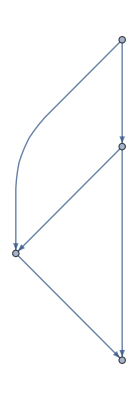

```mathematica
AdjacencyGraph[({{0, 0, 1, 0}, {1, 0, 0, 1}, {0, 0, 0, 0}, {1, 0, 1, 0}})]
```

```mathematica
EdgeList[AdjacencyGraph[({{0, 0, 1, 0}, {1, 0, 0, 1}, {0, 0, 0, 0}, {1, 0, 1, 0}})]]
```

{1->3,2->1,2->4,4->1,4->3}

```mathematica
N@MDLScore[EdgeList[AdjacencyGraph[({{0, 0, 1, 0}, {1, 0, 0, 1}, {0, 0, 0, 0}, {1, 0, 1, 0}})]],testData]
```

515.86

```mathematica
N@MDLScore[{},testData]
```

25.8233

## Cálculo de rendimiento

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
EvaluateGenome[dataset_,population_, ScoreFunction_ : MDLScore]:=ProgressParallelMap[
<|
"Genome"->#,
"Score"->N@ScoreFunction[EdgeList[AdjacencyGraph[#]],dataset]
|>&,
population,
Method->"CoarsestGrained",
"Label"->"Evaluating population"
];
EvaluateGenome[dataset_,population_,minibatchSize_ ,ScoreFunction_ : MDLScore]:=ProgressParallelMap[
<|
"Genome"->#,
"Score"->N@ScoreFunction[EdgeList[AdjacencyGraph[#]],RandomSample[dataset,minibatchSize]]
|>&,
population,
Method->"CoarsestGrained",
"Label"->"Evaluating population"
];
```

```mathematica
EvaluateGenome[testData,{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},MDLScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→524.761|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→489.269|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→467.979|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→553.659|>}

```mathematica
EvaluateGenome[testData,{({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}}),({{0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 1, 0}}),({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}})},CorrectlyClassifiedPercentageScore]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→0.953333|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→0.953333|>,<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→0.586667|>,<|Genome→{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},Score→0.953333|>}

## Selección

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateSelection[evaluatedGenome_,n_,"LessIsBetter"]:= Part[SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]];
ProportionateSelection[evaluatedGenome_,n_,"MoreIsBetter"]:= Part[Reverse[SortBy[evaluatedGenome,Key["Score"]]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]]
```

```mathematica
ProportionateSelection[
{
<|"Genome"->{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},"Score"->524.7610289505521|>,
<|"Genome"->{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},"Score"->489.268798358215|>,
<|"Genome"->{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},"Score"->632.7710420740774|>,
<|"Genome"->{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},"Score"->553.6591790004508|>
},2,"LessIsBetter"]
```

{<|Genome→{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},Score→524.761|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→489.269|>}

```mathematica
ProportionateSelection[
{
<|"Genome"->{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,1,1,0}},"Score"->0.9533333333333334|>,<|"Genome"->{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},"Score"->0.9533333333333334|>,<|"Genome"->{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},"Score"->0.5866666666666667|>,<|"Genome"->{{0,0,0,1},{1,0,1,0},{0,0,0,1},{0,0,0,0}},"Score"->0.9533333333333334|>
},2,"MoreIsBetter"]
```

{<|Genome→{{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,1,0,0}},Score→0.586667|>,<|Genome→{{0,1,0,0},{0,0,0,0},{0,0,0,0},{1,0,1,0}},Score→0.953333|>}

## Crossover

```mathematica
RandomCrossover[parent1_,parent2_]:=Block[{vector1,vector2,transformed},
vector1 =Flatten[parent1];
vector2 =Flatten[parent2];
transformed = Table[If[RandomInteger[]==1,vector1[[i]],vector2[[i]]],{i,1,Length[vector1]}];
SimplifyToDAG[Partition[transformed,Length[parent1]]]
];
```

```mathematica
PopulationCrossover[population_,childrenPerCouple_]:=Block[{couples,newGeneration},
couples = Partition[RandomSample[population],2];
newGeneration = Flatten[
Map[
Table[RandomCrossover[First[#],Last[#]],childrenPerCouple]&,
couples
],1];
Return[newGeneration];
];
```

```mathematica
Map[MatrixForm,PopulationCrossover[{({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 1, 0}})},5]]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

## Mutación

```mathematica
Flip[0]=1;
Flip[1] = 0;

RandomMutate[matrix_,probability_]:=Block[{newList,index,newMatrix},
If[RandomReal[]<probability,
newList = Flatten[matrix];
index = RandomInteger[{1,Length[newList]}];
newList = MapAt[Flip,newList, index];
newMatrix = Partition[newList,Length[matrix]];
Return[SimplifyToDAG[newMatrix]];
,
Return[matrix]
]
];
PopulationMutate[population_,probability_]:=Map[RandomMutate[#,probability]&,population];
```

```mathematica
Map[MatrixForm,PopulationMutate[{({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 1}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}}),({{0, 0, 0, 1}, {1, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}})},0.8]]
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

## Algoritmo principal

```mathematica
SelectBest[population_, n_ : 1, "LessIsBetter"]:=MinimalBy[population,Key["Score"],n];
SelectBest[population_, n_ : 1, "MoreIsBetter"]:=MaximalBy[population,Key["Score"],n];

GenerateInitialPopulation[n_,size_,dataset_, ScoreFunction_ ]:=EvaluateGenome[dataset,GeneratePopulation[n,size],ScoreFunction];
GenerateInitialPopulation[n_,size_,dataset_,minibatchSize_, ScoreFunction_ ]:=EvaluateGenome[dataset,GeneratePopulation[n,size],minibatchSize,ScoreFunction];

Generation[dataset_,population_,survivors_,mutationProb_,ScoringFunction_,scoreType_,minibatchSize_ : None]:=Block[{setMinibatchSize,populationSize,childrenPerCouple,fittest,newGeneration,mutated},
setMinibatchSize = If[minibatchSize===None || minibatchSize>Length[dataset],Length[dataset],minibatchSize];
populationSize = Length[population];
childrenPerCouple = (2 populationSize)/survivors;
fittest = ProportionateSelection[population,survivors,scoreType];
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb];
EvaluateGenome[dataset,mutated,setMinibatchSize,ScoringFunction]
];
GeneticAlgorithm[dataset_,population_,survivors_,mutationProb_,ScoringFunction_,scoreType_,generations_,minibatchSize_ : None]:=
ProgressNestList[Generation[dataset,#,survivors,mutationProb,ScoringFunction,scoreType,minibatchSize]&,population,generations,"Label"->"Generation"];
```

```mathematica
PlotBayesNet[net_,attributes_]:=AdjacencyGraph[
net["Genome"],
PlotLabel->net["Score"],
PlotTheme->"ClassicDiagram",
VertexLabels->MapIndexed[First[#2]->#1&,attributes],
VertexSize->Medium,
ImageSize->{400,400},
PlotRangePadding->Scaled[0.2],
Frame->True
];
PlotGeneration[generation_,attributes_,index_]:=Labeled[Map[PlotBayesNet[#,attributes]&,generation],"Generation "<>ToString[index],Top]
```

### Ejemplo

```mathematica
{{attributes},testData} = TakeDrop[Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Discretized","iris.csv"}]],1];
```

```mathematica
population = GenerateInitialPopulation[4,50,testData,MDLScore];
```

```mathematica
result = GeneticAlgorithm[testData,population,10,0.5,MDLScore,"LessIsBetter",50];
```

```mathematica
fittestByGeneration = Map[SelectBest[#,3,"LessIsBetter"]&,result];
```

```mathematica
generationPlots = MapIndexed[PlotGeneration[#1,attributes,First[#2]]&,fittestByGeneration];
```

```mathematica
scoreVsK = Table[{k,Mean[result[[k]][[All,"Score"]]]},{k,1,Length[result]}];
```

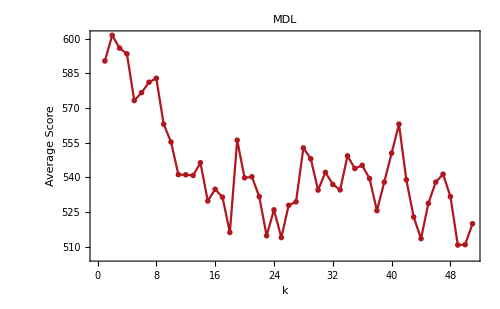

```mathematica
ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"MDL",
Frame->True,
ImageSize->500
]
```

## Entrenamiento

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
BayesGeneticTrainAndPlot[datasetPath_,populationSize_,survivors_,mutationProb_,ScoringFunction_,scoreType_,generations_,minibatchSize_ : None]:=Block[{setMinibatchSize,attributes,dataset,population,iterations,fittestByGeneration,generationPlots,scoreVsK,scoreVsKPlot},

{{attributes},dataset} = TakeDrop[Import[datasetPath],1];
setMinibatchSize = If[minibatchSize===None|| minibatchSize>Length[dataset],Length[dataset],minibatchSize];
population = GenerateInitialPopulation[Length[attributes],populationSize,dataset,setMinibatchSize,ScoringFunction];
iterations = GeneticAlgorithm[dataset,population,survivors,mutationProb,ScoringFunction,scoreType,generations,setMinibatchSize];
fittestByGeneration = Map[SelectBest[#,3,scoreType]&,iterations];
generationPlots = MapIndexed[PlotGeneration[#1,attributes,First[#2]]&,fittestByGeneration];

scoreVsK = Table[{k,Mean[iterations[[k]][[All,"Score"]]]},{k,1,Length[iterations]}];
scoreVsKPlot = ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->ToString[ScoringFunction],
Frame->True,
ImageSize->500
];

{generationPlots,scoreVsKPlot}
];
BayesGeneticTrainAndExportPlots[datasetPath_,populationSize_,survivors_,mutationProb_,ScoringFunction_,scoreType_,generations_,minibatchSize_ : None]:=Block[{generationPlots,scoreVsKPlot},
{generationPlots,scoreVsKPlot} = BayesGeneticTrainAndPlot[datasetPath,populationSize,survivors,mutationProb,ScoringFunction,scoreType,generations,minibatchSize];
CreateDirectory[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath]}]];
Export[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"ScoreVsK.png"}],scoreVsKPlot];
ExportImages[FileNameJoin[{NotebookDirectory[],FileBaseName[datasetPath],"imgs.png"}],generationPlots];
];
```

### Test Iris dataset

```mathematica
BayesGeneticTrainAndExportPlots[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Discretized","bank.csv"}],
50,8,0.3,MDLScore,"LessIsBetter",100,500
];
```

$Aborted

### Test all datasets

```mathematica
ProgressMap[
BayesGeneticTrainAndExportPlots[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Discretized",#}],
50,10,0.5,MDLScore,"LessIsBetter",40,500
]&,
{"iris.csv","car.csv","bank.csv","adult.csv"},
"Label"->"Testing dataset"
]
```

{Null,Null,Null,Null}